```mathematica
A=2*Pi* 440;
```

```mathematica
Sound[{Play[Sin[A*t], {t,0,1}],Play[Sin[2^(4/12)*A*t], {t,0,1}], Play[Sin[A*t]+Sin[2^(4/12)*A*t], {t,0,2}]}]
```

-Graphics-

```mathematica
Sound[{Play[Sin[A*t], {t,0,1}],Play[Sin[81/64*A*t], {t,0,1}], Play[Sin[A*t]+Sin[81/64*A*t], {t,0,2}]}]
```

-Graphics-

```mathematica
Sound[{Play[Sin[2^(4/12)*A*t], {t,0,1}],Play[Sin[81/64*A*t], {t,0,1}], 
Play[Sin[2^(4/12)*A*t]+Sin[81/64*A*t], {t,0,5}]}]
```

-Graphics-

```mathematica
Sound[{Play[Sin[2^(4/12)*A*t], {t,0,1}],Play[Sin[81/64*A*t], {t,0,1}], 
Play[2*Sin[A*t]+Sin[2^(4/12)*A*t]+Sin[81/64*A*t], {t,0,5}]}]
```

-Graphics-

Now for 5ths

```mathematica
Sound[{Play[Sin[A*t], {t,0,1}],Play[Sin[2^(7/12)*A*t], {t,0,1}], Play[Sin[A*t]+Sin[2^(7/12)*A*t], {t,0,3}]}]
```

-Graphics-

```mathematica
Sound[{Play[Sin[A*t], {t,0,1}],Play[Sin[3/2*A*t], {t,0,1}], Play[Sin[A*t]+Sin[3/2*A*t], {t,0,3}]}]
```

-Graphics-

```mathematica
Sound[{Play[Sin[2^(7/12)*A*t], {t,0,1}],Play[Sin[3/2*A*t], {t,0,1}], 
Play[Sin[2^(7/12)*A*t]+Sin[3/2*A*t], {t,0,5}]}]
```

-Graphics-

```mathematica
Sound[{
Play[5*Sin[A*t]+5*Sin[2^(7/12)*A*t]+0*Sin[3/2*A*t], {t,0,5}]}]
```

-Graphics-

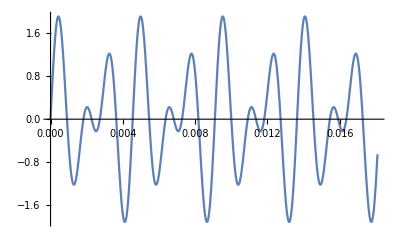

```mathematica
Plot[Sin[A*t]+Sin[3/2*A*t], {t,0,50/A}]
```

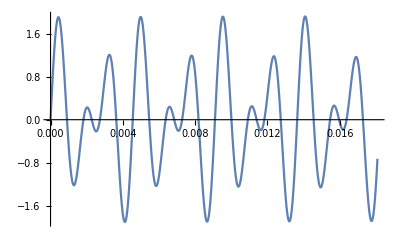

```mathematica
Plot[Sin[A*t]+Sin[2^(7/12)*A*t], {t,0,50/A}]
```

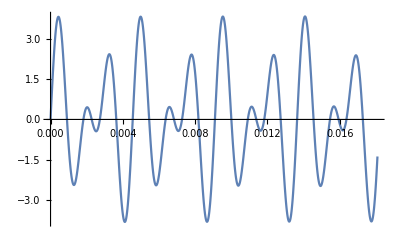

```mathematica
Plot[2*Sin[A*t]+Sin[2^(7/12)*A*t]+Sin[3/2*A*t], {t,0,50/A}]
```